0.635028

0.297928

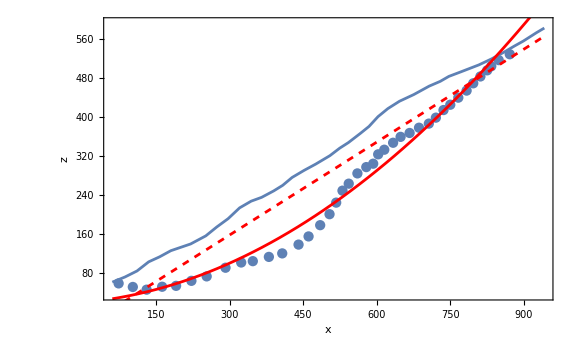

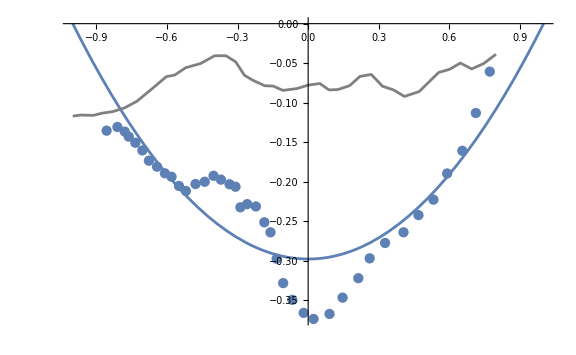

```mathematica
data=Import[NotebookDirectory[]<>"data/LandslideFailureSurfaces.xlsx"];
(*Extract first sheet*)
sheetdata=data[[1]];
(*Take rows 2 to end,first two columns*)
plotDataB=sheetdata[[2;;,1;;2]];  (*rows 2 to end,columns 1 and 2*)
plotDataH=sheetdata[[2;;,3;;4]];  (*rows 2 to end,columns 1 and 2*)
pts = plotDataB;
pts=Select[plotDataB,!AllTrue[#,#===""||#===Null&]&];(*data cleaning*)
ptsH=Select[plotDataH,!AllTrue[#,#===""||#===Null&]&];(*data cleaning*)
(*pts={{x1,z1},{x2,z2},...}*)
xData=Join[pts[[All,1]],ptsH[[All,1]]];
zData=Join[pts[[All,2]],ptsH[[All,2]]];
(*xData=pts[[All,1]];
zData=pts[[All,2]];*)

linFit=Fit[Transpose[{xData,zData}],{1,x},x];
α=Coefficient[linFit,x,1] (*linear term*)

residuals=pts[[All,2]]-(linFit/. x->pts[[All,1]]);
quadFit=Fit[Transpose[{pts[[All,1]],residuals}],{1,x,x^2},x];
a=Coefficient[quadFit,x,0];  (*constant term*)
b=Coefficient[quadFit,x,1];  (*linear term*)
c=Coefficient[quadFit,x,2];  (*quadratic term*)
(*convert to form we care about*)
x0=-b/(2 c);
Lx=Max[Abs[xData-x0]];(*Sqrt[x0/c];*)
δb=quadFit/.x->x0+Lx;
b0=b^2/(4 c)-a +δb;
(*{x0,b0,Lx}*)
b0/Lx

p1=ListPlot[{pts},Frame->True,FrameLabel->{"x","z"}];
p2=ListLinePlot[{plotDataH}];
p3=Plot[linFit+quadFit,{x,Min[xData],Max[xData]},PlotStyle->{Red}];
p4=Plot[linFit,{x,Min[xData],Max[xData]},PlotStyle->{Red,Dashed}];
Show[p1,p2,p3,p4,ImageSize->Large,PlotRange->{Min[zData]-10,Max[zData]+10}]

(*plot rescaled quadratic geometry*)
qF=quadFit/.{x->(x+x0)/Lx};
p1=ListPlot[Transpose[{-Sign[α]*(pts[[All,1]]-x0)/Lx,(residuals-δb)/Lx}]];
p2 = Plot[b0/Lx*(x^2-1),{x,-1,1}];

(*Select and plot points from the free surface*)
residuals=ptsH[[All,2]]-(linFit/. x->ptsH[[All,1]]);
p3=ListLinePlot[Transpose[{-Sign[α]*(ptsH[[All,1]]-x0)/Lx,(residuals-δb)/Lx}],PlotStyle->Gray];
Show[p1,p2,p3,PlotRange->All]
```

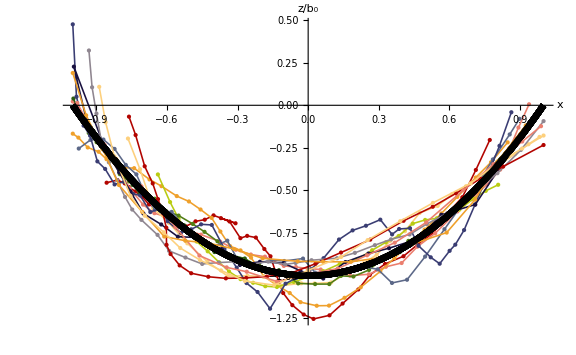

/Users/mallickrishg/Documents/GitHub/landslides/analyticsol/b0EnsemblePlot.jpg

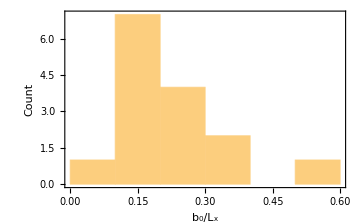

```mathematica
(*Function to process one sheet*)
Get[NotebookDirectory[]<>"LandslideProcessor.wl"]
data=Import[NotebookDirectory[]<>"data/LandslideFailureSurfaces.xlsx"];

(*Process all 15 sheets*)
processed=processSheet/@data[[1;;15]];

(*Extract important quantities*)
rescaledB=processed[[All,1]];
rescaledH=processed[[All,2]];
fits=processed[[All,3]];
b0vals = processed[[All,4]];
αvals = processed[[All,5]];

(*Plot all fitted parabolas together*)
(*Build combined plot*)
fig=Show[Table[
{ListLinePlot[Transpose[{rescaledB[[i]][[All,1]],rescaledB[[i]][[All,2]]/b0vals[[i]]}],
Mesh->All,
PlotStyle->{ColorData[10][i],Thickness[0.002],PointSize[Medium]}],
Plot[fits[[i]][x],{x,-1,1},
PlotStyle->{Black,Thickness[0.008]}]},
{i,Length[processed]}]//Flatten,
AxesLabel->{Style["x",35],Style[Row[{"z/" ,Subscript["b","0"]}],35]},FontSize->25,
PlotRange->All,ImageSize->Large,
LabelStyle->Directive[FontSize->20]]
Export[NotebookDirectory[]<>"b0EnsemblePlot.jpg",fig,"JPEG"]

p1=Histogram[b0vals,5,(*number of bins–adjust as you like*)
ChartStyle->Automatic,Frame->True,FrameLabel->{Style[Row[{Subscript["b","0"],"/",Subscript["L","x"]}],20],Style["Count",20]},LabelStyle->Directive[FontSize->20],ImageSize->Medium];
p2=Histogram[Abs[αvals],8,(*number of bins–adjust as you like*)
ChartStyle->Automatic,Frame->True,FrameLabel->{Style["α",20],Style["Count",20]},LabelStyle->Directive[FontSize->20],ImageSize->Medium];
Show[p1]
```

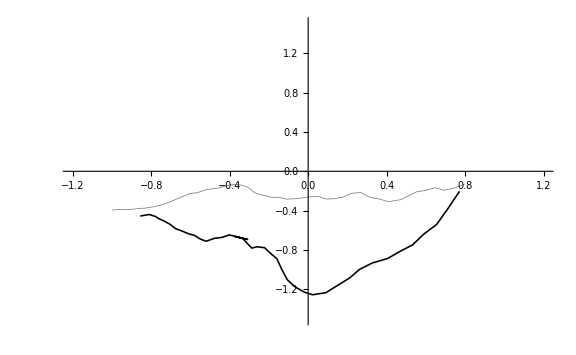

```mathematica
Show[ListLinePlot[rescaledH[[1;;1]],PlotStyle->{{Gray,Thickness[0.001]}}],
ListLinePlot[rescaledB[[1;;1]],PlotStyle->{{Black,Thickness[0.002],PointSize->Small}}],
PlotRange->{{-1.2,1.2},{-1.5,1.5}},ImageSize->Large]
```